```mathematica
(*************************  NIPOTI  ************************)
Manipulate[
coloreDenominatore = Blue;
coloreNumeratore = Red;
spaceX = 5;
objBottiglie = {};
plotRange = 15;
offsetX = -19;
offsetY = 3;
For[i = 0, i< numeroNipoti,i++,
AppendTo[objBottiglie,
{Thickness[.01],
Line[{{0 + (i*spaceX)+offsetX,0},{2 + (i*spaceX)+offsetX,4}}],(*Gamba destra*)
Line[{{2 + (i*spaceX)+offsetX,4},{4 + (i*spaceX)+offsetX,0}}],(*Gamba sinistra*)
Line[{{2 + (i*spaceX)+offsetX,4},{2 + (i*spaceX)+offsetX,8}}], (*Busto*)
Line[{{2 + (i*spaceX)+offsetX,8},{0 + (i*spaceX)+offsetX,5}}],
Line[{{2 + (i*spaceX)+offsetX,8},{4 + (i*spaceX)+offsetX,5}}],
Circle[{2 + (i*spaceX)+offsetX,9},1]

}]
(*{Black,Rectangle[{(i*spaceX)+offsetX,0},{3+(i*spaceX)+ offsetX,6}], Disk[{1.5+ (i*spaceX)+offsetX, 6}, 1.5], Black, Rectangle[{1+(i*spaceX)+offsetX,7},{2+ (i*spaceX)+offsetX,9}]}}*)
];
objBicchieri = {};
offsetX = -9;
offsetY = -6;
For[i = 0, i< numeroBicchieri,i++,
AppendTo[objBicchieri,{Black,Circle[{(i*2)+offsetX,0 + offsetY},1]}]
];
Graphics[{
objBottiglie,
objBicchieri
},PlotRange->{{-20,25},{-15,15}}]
(*paramentri primo slider*)
,{
{numeroNipoti,1,(*valore iniziale slider numeratore*)
		Style["Numero bottiglie",Directive[coloreNumeratore,Large]]},
	1,8,1,(*valore iniziale, valore finale, step di incremento/decremento slider*)
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},
	LabelStyle->Directive[coloreNumeratore,Large],
	ImageSize->170
	},(*--fine slider numeratore*)
{
{numeroBicchieri,2,Style["Numero bicchieri",Directive[coloreDenominatore,Large]]}
,1,10,1,
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},(*rimuovo tutto tranne l'inputField*)
	LabelStyle->Directive[coloreDenominatore,Large],ImageSize->170}
]
```

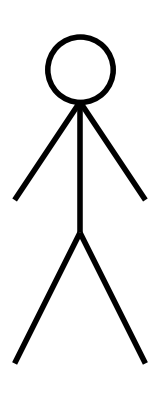

```mathematica
Graphics[{Thickness[.01],
Line[{{0,0},{2,4}}],(*Gamba destra*)
Line[{{2,4},{4,0}}],(*Gamba sinistra*)
Line[{{2,4},{2,8}}], (*Busto*)
Line[{{2,8},{0,5}}],
Line[{{2,8},{4,5}}],
Circle[{2,9},1]

}, PlotRange-> Automatic]
```